```mathematica
alckminScore :=  4113*a + 4165*b + 514
bolsonaroScore := 392a + 521b + 4992
ciroScore := 4387a + 3612b + 1341
haddadScore := 1109*a + 1703*b + 3154
```

```mathematica
getVReg[conditionList_] :=  Reduce [{conditionList, a≥ 0, b≥0, 1≥a, 1 ≥b, a≥b }, {a,b}]
vicRegplt[vreg_] := RegionPlot[vreg, {a,0,1}, {b,0,1}]
propVic[vreg_]:= N[Area[Region[ImplicitRegion[vreg,{a,b}]]]] * 2
```

```mathematica
propVic[getVReg[ciroScore ≥haddadScore]]
```

0.755121

```mathematica
scores :=  {alckminScore,bolsonaroScore,ciroScore, haddadScore}
```

```mathematica
quantiCounter[actorScore_] := propVic[getVReg[actorScore > #]] &/@ scores
```

```mathematica
quantiCounter /@ scores  // MatrixForm
```

(0. | 0.310558 | 0. | 0.575539
0.689442 | 0. | 0.470875 | 0.998342
1. | 0.529125 | 0. | 0.806683
0.424461 | 0.00165774 | 0.193317 | 0.)

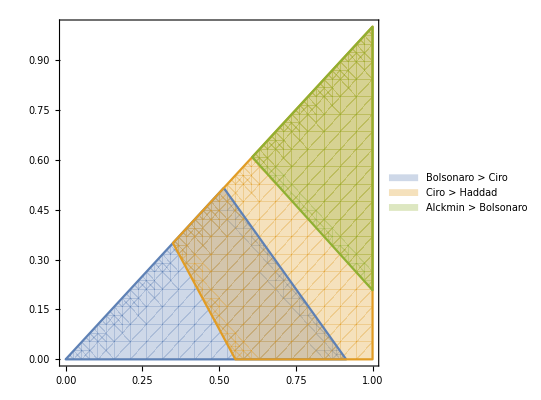

```mathematica
RegionPlot[{Evaluate[getVReg[bolsonaroScore ≥ciroScore]],
 Evaluate[getVReg[ciroScore > haddadScore]],
 Evaluate[getVReg[alckminScore > bolsonaroScore]],
 }, {a,0,1}, {b,0,1}, PlotLegends -> {"Bolsonaro > Ciro", "Ciro > Haddad", "Alckmin > Bolsonaro"} ]
```

```mathematica
ClearAll[hatchedTexture]
hatchedTexture1[ps_: None, cols_: {Black},
  t_: AbsoluteThickness[10]] := 
 RegionPlot[True, {x, 0, 1}, {y, 0, 1}, 
  MeshFunctions -> {#1 + #2 &}, Mesh -> 10, MeshShading -> None, 
  MeshStyle -> {Directive[t, #] & /@ {Black}}, Frame -> False, 
  PlotRangePadding -> 0, PlotStyle -> ps, BaseStyle -> EdgeForm[], 
  BoundaryStyle -> None]
texture1 := Texture[Rasterize @ hatchedTexture1[ ]];
legendmarker1 := Graphics[{texture1, Polygon[coords = {{0, 0}, {1, 0}, {1, 1}, {0, 1}}, 
     VertexTextureCoordinates -> (coords/2)]}]
     
hatchedTexture2[ps_: None, cols_: {Black},
  t_: AbsoluteThickness[10]] := 
 RegionPlot[True, {x, 0, 1}, {y, 0, 1}, 
  MeshFunctions -> { #1 &}, Mesh -> 10, MeshShading -> None, 
  MeshStyle -> {Directive[t, #] & /@ {Black}}, Frame -> False, 
  PlotRangePadding -> 0, PlotStyle -> ps, BaseStyle -> EdgeForm[], 
  BoundaryStyle -> None]
texture2 := Texture[Rasterize @ hatchedTexture2[ ]];
legendmarker2 := Graphics[{texture2, Polygon[coords = {{0, 0}, {1, 0}, {1, 1}, {0, 1}}, 
     VertexTextureCoordinates -> (coords/2)]}]
     
hatchedTexture3[ps_: None, cols_: {Black},
  t_: AbsoluteThickness[10]] := 
 RegionPlot[True, {x, 0, 1}, {y, 0, 1}, 
  MeshFunctions -> {#1 - #2 &} , Mesh -> 10, MeshShading -> None, 
  MeshStyle -> {Directive[t, #] & /@ {Black}}, Frame -> False, 
  PlotRangePadding -> 0, PlotStyle -> ps, BaseStyle -> EdgeForm[], 
  BoundaryStyle -> None]
texture3 := Texture[Rasterize @ hatchedTexture3[ ]];
legendmarker3 := Graphics[{texture3, Polygon[coords = {{0, 0}, {1, 0}, {1, 1}, {0, 1}}, 
     VertexTextureCoordinates -> (coords/2)]}]
```

```mathematica
texture2
```

Texture[-Graphics-]

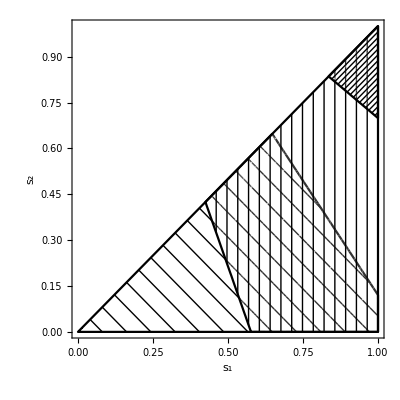

```mathematica
Show[
  RegionPlot[{Evaluate[getVReg[bolsonaroScore ≥ciroScore]]}, {a,0,1}, {b,0,1} ,MeshFunctions -> {#1 + #2 &} , Mesh ->15, MeshStyle -> {Black} ,BoundaryStyle ->{Thick,Black}, PlotStyle ->{Opacity[0.2], White}, PlotLegends -> SwatchLegend[ {Black}, {"Bolsonaro > Ciro"}, LegendMarkerSize -> {{30, 30}}, LegendMarkers -> legendmarker1, LabelStyle -> 15], FrameLabel->{Text[Style[Subscript["s", "1"], Large]],Text[Style[Subscript["s", "2"], Large]]}] ,
   
   RegionPlot[{Evaluate[getVReg[ciroScore ≥haddadScore]]}, {a,0,1}, {b,0,1}, MeshFunctions -> { #1 &}, Mesh -> 15, MeshStyle -> {Black},BoundaryStyle ->{Thick,Black},  PlotStyle ->{Opacity[0.2],White} ,  PlotLegends -> SwatchLegend[ {Black},{"Ciro > Haddad"} , LegendMarkerSize -> {{30, 30}}, LegendMarkers -> legendmarker2, LabelStyle -> 15] ],
    
    RegionPlot[{Evaluate[getVReg[alckminScore > bolsonaroScore]]}, {a,0,1}, {b,0,1}, MeshFunctions -> { #1 - #2 &}, Mesh -> 15, MeshStyle -> {Black},BoundaryStyle ->{Thick,Black},  PlotStyle ->{Opacity[0.2],White} ,  PlotLegends -> SwatchLegend[ {Black},{"Alckmin>Bolsonaro"} , LegendMarkerSize -> {{30, 30}}, LegendMarkers -> legendmarker3, LabelStyle -> 15] ]]
```